```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
On[Assert]
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics"],FontFamily->"Times"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]];
```

```mathematica
qns={{{"J","P","L","S","e"},{1/2,+1,0,1/2,0},{1/2,+1,1,1/2,0},{1/2,+1,1,3/2,0},{1/2,+1,2,3/2,0}},{{"J","P","L","S","e"},{3/2,+1,1,1/2,0},{3/2,+1,2,1/2,0},{3/2,+1,0,3/2,0},{3/2,+1,1,3/2,0},{3/2,+1,2,3/2,0},{3/2,+1,3,3/2,0}},{{"J","P","L","S","e"},{5/2,+1,2,1/2,0},{5/2,+1,3,1/2,0},{5/2,+1,1,3/2,0},{5/2,+1,2,3/2,0},{5/2,+1,3,3/2,0},{5/2,+1,4,3/2,0}},{{"J","P","L","S","e"},{7/2,+1,3,1/2,0},{7/2,+1,4,1/2,0},{7/2,+1,2,3/2,0},{7/2,+1,3,3/2,0},{7/2,+1,4,3/2,0},{7/2,+1,5,3/2,0}},{{"J","P","L","S","e"},{1/2,-1,1,1/2,0},{1/2,-1,1,3/2,0},{1/2,-1,2,3/2,0}},{{"J","P","L","S","e"},{3/2,-1,1,1/2,0},{3/2,-1,2,1/2,0},{3/2,-1,1,3/2,0},{3/2,-1,2,3/2,0},{3/2,-1,3,3/2,0}},{{"J","P","L","S","e"},{5/2,-1,2,1/2,0},{5/2,-1,3,1/2,0},{5/2,-1,1,3/2,0},{5/2,-1,2,3/2,0},{5/2,-1,3,3/2,0},{5/2,-1,4,3/2,0}},{{"J","P","L","S","e"},{7/2,-1,3,1/2,0},{7/2,-1,4,1/2,0},{7/2,-1,2,3/2,0},{7/2,-1,3,3/2,0},{7/2,-1,4,3/2,0},{7/2,-1,5,3/2,0}}};
```

```mathematica
For[iqn=1,iqn≤Length[qns],iqn++,

Print[iqn];
qn=qns[[iqn]];
whichBellow={};
startCondition=1;

While[Length[whichBellow]≠0+startCondition,
For[iBelow=1,iBelow≤Length[whichBellow],iBelow++,
pos=whichBellow[[iBelow]];
qn[[pos,5]]+=1
];
startCondition=0;
whichBellow={};

For[ep=2,ep≤Length[qn],ep++,
Print[ToString[ep]<>"/"<>ToString[Length[qn]]];
ClearAll[J,P,Isospin,γMax,Λ,m1,m2,m3,projector,project,size,firstNonZero,ham,sM,t1,t2];
(**** !!!TUNABLE PARAMETERS!!! ****)
J=qn[[ep,1]];(* Total angular momentum J = Λ + S *)
P=qn[[ep,2]];(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=1;(* Isospin, 0 means flavour antisymmetric, 1 means symmetric *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=qn[[ep,3]];(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=qn[[ep,4]];(* Total spin *)
m1=sq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=bq;(* mass of quark 3 *)
excited=qn[[ep,5]];(* Choose excited state, 0 for ground state *)
groundMass=6.033;
save=True;(* Do you want to save parameters and mass to csv file? *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
project=If[m1==m2,True,False];
(* Obtain projector matrix *)
projector=Projector[J,P,Λ,S,γMax,Isospin];
(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];
(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
firstNonZero=If[project==True,size-Total[Diagonal[projector]]+excited+1,1+excited];
ham[ω_]:=Hb[J,P,Isospin,Λ,S,γMax,ω,m1,m2,m3,project];
sM=stateMatrix[J,P,Λ,S,γMax];
Print[sM//Length];
(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,firstNonZero,0.1,0.8,0.0005]];
wMin=(a+b)/2;
eigvalMin=Eigenvalues[ham[wMin]][[-firstNonZero]];
If[eigvalMin<groundMass+0.8,AppendTo[whichBellow,ep]];
Print["{ω_min,E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
(* Save data *)
If[save,
dataset=Import["ladders.mx"];
quarkDict=Association[{uq->"u",sq->"s",cq->"c",bq->"b"}];
If[Isospin==0&&m1==uq&&m2==uq,secondQuark="d",secondQuark=quarkDict[m2]];
quarks=quarkDict[m1]<>secondQuark<>quarkDict[m3];
row={quarks,J,Λ,S,P,Isospin,excited,γMax,Round[wMin,0.0001],Round[eigvalMin,0.0001]};
If[MemberQ[dataset,row]==False,AppendTo[dataset,row];Export["ladders.mx",dataset];Print["Entry Added"],Print["Entry Already exists"]];
](* End of if *)
];(* End of ep for loop *)
Print[whichBellow]
](* End of While loop *)
];;(* End of iqn for loop *)
```

{{{0.,5.804},{0.1,5.804}},{{0.,5.9412},{0.1,5.9412}},{{0.,6.3018},{0.1,6.3018}},{{0.,6.4149},{0.1,6.4149}},{{0.,6.4822},{0.1,6.4822}},{{0.,6.5362},{0.1,6.5362}},{{0.,6.5545},{0.1,6.5545}},{{0.,6.5931},{0.1,6.5931}},{{0.,6.6148},{0.1,6.6148}},{{0.,6.6189},{0.1,6.6189}},{{0.,6.6458},{0.1,6.6458}},{{0.,6.6681},{0.1,6.6681}},{{0.13,5.9718},{0.23,5.9718}},{{0.13,6.3594},{0.23,6.3594}},{{0.13,6.4325},{0.23,6.4325}},{{0.13,6.4727},{0.23,6.4727}},{{0.13,6.4822},{0.23,6.4822}},{{0.13,6.5741},{0.23,6.5741}},{{0.13,6.5818},{0.23,6.5818}},{{0.13,6.6031},{0.23,6.6031}},{{0.13,6.6148},{0.23,6.6148}},{{0.13,6.6189},{0.23,6.6189}},{{0.13,6.6458},{0.23,6.6458}},{{0.13,6.6823},{0.23,6.6823}},{{0.13,6.7157},{0.23,6.7157}},{{0.13,7.0607},{0.23,7.0607}},{{0.26,6.3594},{0.36,6.3594}},{{0.26,6.4727},{0.36,6.4727}},{{0.26,6.4822},{0.36,6.4822}},{{0.26,6.5818},{0.36,6.5818}},{{0.26,6.6031},{0.36,6.6031}},{{0.26,6.6148},{0.36,6.6148}},{{0.26,6.6458},{0.36,6.6458}},{{0.26,6.7157},{0.36,6.7157}},{{0.26,6.8903},{0.36,6.8903}},{{0.26,7.0422},{0.36,7.0422}},{{0.26,7.0607},{0.36,7.0607}},{{0.39,6.4822},{0.49,6.4822}},{{0.39,6.6148},{0.49,6.6148}},{{0.39,6.7947},{0.49,6.7947}},{{0.39,6.8903},{0.49,6.8903}},{{0.39,7.0422},{0.49,7.0422}},{{0.39,7.0607},{0.49,7.0607}},{{0.39,7.4341},{0.49,7.4341}},{{0.62,6.1093},{0.72,6.1093}},{{0.62,6.2329},{0.72,6.2329}},{{0.62,6.2485},{0.72,6.2485}},{{0.62,6.3387},{0.72,6.3387}},{{0.62,6.3572},{0.72,6.3572}},{{0.62,6.3758},{0.72,6.3758}},{{0.62,6.5394},{0.72,6.5394}},{{0.62,6.639},{0.72,6.639}},{{0.62,6.6499},{0.72,6.6499}},{{0.62,6.8627},{0.72,6.8627}},{{0.75,6.1093},{0.85,6.1093}},{{0.75,6.2329},{0.85,6.2329}},{{0.75,6.2485},{0.85,6.2485}},{{0.75,6.3387},{0.85,6.3387}},{{0.75,6.3572},{0.85,6.3572}},{{0.75,6.3758},{0.85,6.3758}},{{0.75,6.5394},{0.85,6.5394}},{{0.75,6.639},{0.85,6.639}},{{0.75,6.6499},{0.85,6.6499}},{{0.75,6.6945},{0.85,6.6945}},{{0.75,6.8412},{0.85,6.8412}},{{0.75,6.8627},{0.85,6.8627}},{{0.88,6.2485},{0.98,6.2485}},{{0.88,6.3758},{0.98,6.3758}},{{0.88,6.5906},{0.98,6.5906}},{{0.88,6.6499},{0.98,6.6499}},{{0.88,6.6883},{0.98,6.6883}},{{0.88,6.6945},{0.98,6.6945}},{{0.88,6.8412},{0.98,6.8412}},{{0.88,6.8627},{0.98,6.8627}},{{0.88,7.2571},{0.98,7.2571}},{{1.01,6.5906},{1.11,6.5906}},{{1.01,6.6883},{1.11,6.6883}},{{1.01,6.6945},{1.11,6.6945}},{{1.01,6.8627},{1.11,6.8627}},{{1.01,7.0848},{1.11,7.0848}},{{1.01,7.2436},{1.11,7.2436}},{{1.01,7.2571},{1.11,7.2571}}}

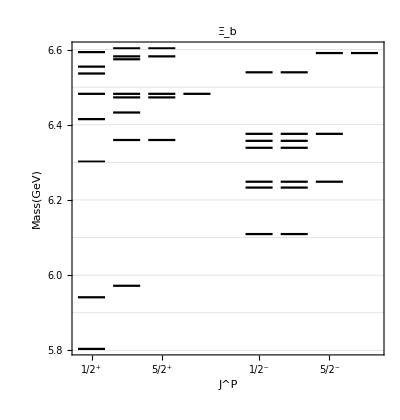

```mathematica
separation=0.13;
length=0.1;
split=0.1;
tower[baryon_,J_,P_,separation_,split_,lineLength_]:=Module[{dataset,list,pAssoc,start},
(* Import dataset of all masses *)
dataset=Import["ladders.mx"];
(* Make a selection of masses based on quantum numbers *)
list=Table[If[dataset[[i+1,1]]==baryon&&dataset[[i+1,8]]>4&&dataset[[i+1,2]]==J&&dataset[[i+1,5]]==P,dataset[[i+1,10]]],{i,1,Length[dataset]-1}];
(* Delete Null cases and sort masses*)
list = DeleteCases[list,Null]//Sort;
pAssoc=<|1->0,-1->4|>;
(* Given J and P determine position of tower *)
j=J-1/2+pAssoc[P];
s=If[P==-1,split,0];
start=j*separation+s;
(* From obtained masses, construct lines *)
lines=Table[{{start,list[[i]]},{start+lineLength,list[[i]]}},{i,1,Length[list]}]
]
mykeTowers[baryon_,separation_,split_,lineLength_]:=Module[{towers,js,ps,i,j,J,P,lines},
towers={};
js={1/2,3/2,5/2,7/2};
ps={1,-1};
For[i=1,i≤Length[ps],i++,
For[j=1,j≤Length[js],j++,
J=js[[j]];
P=ps[[i]];
lines=tower[baryon,J,P,separation,split,lineLength];
For[l=1,l≤Length[lines],l++,AppendTo[towers,lines[[l]]]]
](* End of j loop *)
](* End of i loop *);
Return[towers]
]
towers=mykeTowers["usb",separation,split,length]
ground=towers[[1,1,2]];

fontSize=10;
tick1={0.05,Style["1/2^+",FontSize->fontSize,Black,Bold]};
tick2={0.05+separation,Style["3/2^+",FontSize->fontSize,Black,Bold]};
tick3={0.05+2*separation,Style["5/2^+",FontSize->fontSize,Black,Bold]};
tick4={0.05+3*separation,Style["7/2^+",FontSize->fontSize,Black,Bold]};
tick5={0.05+4*separation+split,Style["1/2^-",FontSize->fontSize,Black,Bold]};
tick6={0.05+5*separation+split,Style["3/2^-",FontSize->fontSize,Black,Bold]};
tick7={0.05+6*separation+split,Style["5/2^-",FontSize->fontSize,Black,Bold]};
tick8={0.05+7*separation+split,Style["7/2^-",FontSize->fontSize,Black,Bold]};

lowest=towers[[1,1,2]];
yMin=Ceiling[lowest,-0.1];
yMax=yMin+0.8;
ticks[min_,max_]:=Module[{d=FindDivisions[{min,max},6],n},n=Ceiling@Log10@Max@Denominator@d;{#,NumberForm[#,{∞,n}]}&/@N@d]
t=ticks[yMin,yMax];

frameTicks={{t,Automatic},{{tick1,tick2,tick3,tick4,tick5,tick6,tick7,tick8},None}};

plot=ListPlot[towers,
Joined->True,
PlotRange->{{0,0.05+7*separation+split+0.05},{lowest,lowest+0.8}},
PlotStyle->{Black},
Frame->{{True,True},{True,False}},
FrameTicks->frameTicks,
GridLines->{None,Table[x,{x,yMin,yMax,0.1}](*Table[ground+0.1*x,{x,0,10}]*)},
GridLinesStyle->{LightGray,Dashed},
FrameLabel->{Style["J^P",FontSize->12],Style["Mass(GeV)",FontSize->12]},
PlotLabel->Style["Ξ_b",FontSize->16,FontFamily->"Times",Black],
AspectRatio->1.05]
```

```mathematica
Export["plots/Silvestre/towers/usb.pdf",plot,"PDF","AllowRasterization"->False]
```

plots/Silvestre/towers/usb.pdf